```mathematica
<<ChipDesigner4`
Off[FindMinimum::lstol]
Off[FindMaximum::lstol]
Off[FindMinimum::fmgz]
Off[FindMaximum::fmgz]
(*Parameters: GND width, DC, Outter RF, RF voltage, RF frq*)
Initialize[25,g,200,250,12]
Manipulate[ShowSecFreq[209,vf,va,2.52]/10^6,{vf,20,80},{va,100,800}]
```

```mathematica
Manipulate[{ShowQ[209,vf,va,2.52],ShowTD[209,vf,va,2.52]},{vf,10,20},{va,100,400}]
```

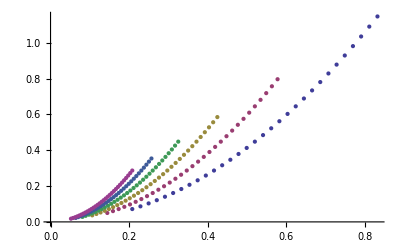

```mathematica
ListPlot[ParallelTable[{ShowQ[209,vf,va,2.52],ShowTD[209,vf,va,2.52]},{vf,10,20,2},{va,100,400,10}]]
```

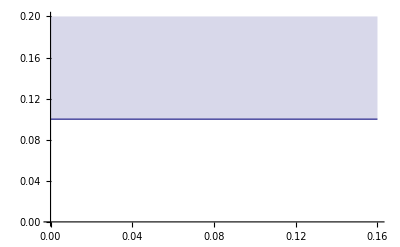

```mathematica
Plot[{x=0.1},{x,0,0.16},Filling->Top]
```

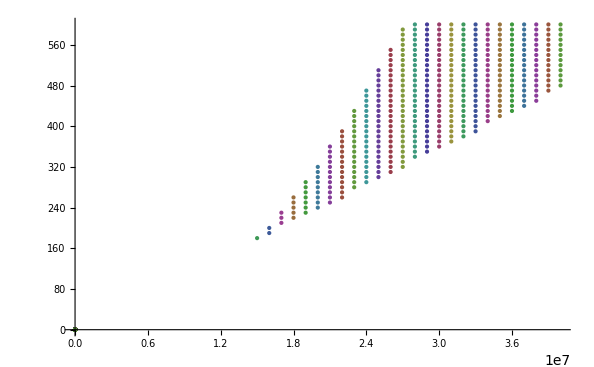

```mathematica
ListPlot[ParallelTable[If[ShowQ[209,vf,va,2.52]<0.17&&ShowTD[209,vf,va,2.52]>0.1,ShowRF[],{0,0}],{vf,12,40,1},{va,50,600,10}]]
```

```mathematica
ParallelTable[If[ShowQ[209,vf/ (2π),va,2.52]<0.17&&ShowTD[209,vf/(2π),va,2.52]>0.1,ShowRF[],{0,0}],{vf,2,180,2},{va,50,800,10}]
```

```mathematica
UNDER CONSTRUCTION
```